# Trajectory Optimization of the Cart - Pole System

## Moving Cart Simulation Function

```mathematica
MOVINGCART[L_, stateFun_, maxT_,scale_]:=Block[{},
(* Controller gives us θ state values at every particular time *)
(* Kinematics takes states and outputs coordinates for joints  *)
state[time_]:=Module[{},
Clear[x,rx,yx];
{px,theta}=(stateFun+{0,0})/.{tt->time};
<|x->px,rx->(px+L*Sin[theta]),ry->-L*Cos[theta]|>
];
frames=Table[Module[{traj=state[t]},
Graphics[{                                             
{Rectangle[{-0.15*L+traj[x],-0.05*L},{0.15*L+traj[x],-0.2*L}],
Rectangle[{-0.05*L+traj[x],-0.05*L},{0.05*L+traj[x],0.05*L}]},     
{Thickness[0.02*L],RGBColor[1/255{250,128,114}],
Line[{{traj[x],0},{traj[rx],traj[ry]}}]},                                
{RGBColor[1/255{19,131,243}], Disk[{traj[x],0},0.05*L]},                  
{RGBColor[1/255{52,73,94}], Disk[{traj[rx],traj[ry]},0.1*L]},
{Blue,Table[Block[{curve=state[τ]},Point[{curve[rx],curve[ry]}]],{τ,0,t,0.01}]}
},PlotRange->scale*{{-1,1},{-1,1}},Background->Lighter[White](*LightBlue*),Axes->{True,True}]]
,{t,0,maxT,maxT/100}];
ListAnimate[frames,AnimationRunning->True]
];
```

## Parameter Initialization

System Dimensions

```mathematica
m1=1; (*Mass of cart*)
m2=0.3; (*Mass of pole*)
L=0.5; (*Length of rod*)
g=9.81; (*Gravity*)
```

Collocation details

```mathematica
tmin=0; (*Time start*)
tmax=5; (*End time*)
n=40;
h=(tmax-tmin)/(n-1); (*Time step*)
```

Path length boundaries

```mathematica
dmin=-2;
dmax=+2;
```

Control Torque boundaries

```mathematica
umin=-20; (*Minimum torque*)
umax=+20; (*Maximum torque*)
```

Initial State

```mathematica
d0=-0.5;
θ0=0;
```

Final State

```mathematica
d=+1.0;
θ=π;
```

## Dynamics, Objectives and Constraints

#### States defined

Cart horizontal position : q1

Pole angle : q2

Cart horizontal velocity : qd1

Pole angular rate : qd2

Cart horizontal acceleration : qdd1

Pole angular acceleration : qdd2

Controller : u

#### Dynamics

```mathematica
q={q1,q2};
qd={qd1,qd2};
qdd={qdd1,qdd2};
M={{m1+m2, m1 L Cos[q2]},{m1 L Cos[q2],m1 L^2}};
R={{0,-m1 qd2 Sin[q2]},{0,0}};
G={{0},{m2 g L Sin[q2]}};
B={{1},{0}};
```

M.qdd + R.qd + G = B*u
ẋ = F[t,x,u]

```mathematica
F[tk_,qk_,uk_]:=Module[{},
{Mm,Rr,Gg,Bb}={M,R,G,B}/.Normal@AssociationThread[{q1,q2,qd1,qd2},qk];
qddk=Inverse[Mm].(Bb*uk-Gg-Rr.qk⟦3;;4⟧);
Flatten[{qk⟦3;;4⟧,qddk}]
]
```

#### Cost Function Description

Minimize the integral of the motor torque square along the entire trajectory

```mathematica
U[tk_,qk_,uk_]:=1/2(m1+m2)qk⟦3⟧^2+m1 qk⟦3⟧ qk⟦4⟧ L Cos[qk⟦2⟧]+1/2 m1 L^2 qk⟦4⟧^2(*+m2 g L Cos[qk⟦2⟧]*);
```

#### Boundary Constraints

Bounds on Initial State

```mathematica
{q10,q20,qd10,qd20}={d0,θ0,0,0};
```

Bounds on Final State

```mathematica
{q1N,q2N,qd1N,qd2N}={d,θ,0,0};
```

#### Path Constraints

Dynamics

M.qdd + R.qd + G == B*u

Keep cart on finite track Length

dmin <= q1 <= dmax

Minimum and Maximum torque from motor

umin <= u <= umax

## Direct Transcription

### Collocation Methods

#### Trapezoidal Collocation

```mathematica
t=Range[tmin,tmax,h];
```

```mathematica
qk0={q10,q20,qd10,qd20};
qkN={q1N,q2N,qd1N,qd2N};
```

```mathematica
ClearAll[qk,uk];
qks=Table[{Subscript[q1k, k],Subscript[q2k, k],Subscript[qd1k, k],Subscript[qd2k, k]},{k,1,n}];
uks=Table[Subscript[uk, k],{k,1,n}];
```

Works with the assumption that the control and the cost function varies linearly between grid points

Cost Function Parameterized

```mathematica
w=MapThread[Function[{tk,qk,uk},U[tk,qk,uk]],{t,qks,uks}];
objPer=Sum[h/2*(w⟦i⟧+w⟦i+1⟧),{i,1,n-1}];
```

System Dynamics Parameterized Constraint

```mathematica
qddkFun[k_]:=h/2*(F[t⟦k⟧,qks⟦k⟧,uks⟦k⟧]+F[t⟦k-1⟧,qks⟦k-1⟧,uks⟦k-1⟧]);
```

#### Hermite - Simpson Collocation

t=Range[tmin,tmax,h/2];

qk0 = {q10, q20, qd10, qd20};
qkN = {q1N, q2N, qd1N, qd2N};

ClearAll[qk,uk];
qks=Table[{q1k_k,q2k_k,qd1k_k,qd2k_k},{k,Length[t]}];
uks=Table[uk_k,{k,Length[t]}];

Cost Function Parameterized

w=MapThread[Function[{tk,qk,uk},U[tk,qk,uk]],{t,qks,uks}];
objPer=Sum[h/6*(w⟦i⟧+4*w⟦i+1⟧+w⟦i+2⟧),{i,1,n-1}];

System Dynamics Parameterized Constraint

qddkFun[k_]:=h/6*(F[t⟦k⟧,qks⟦k⟧,uks⟦k⟧]+F[t⟦k-2⟧,qks⟦k-2⟧,uks⟦k-2⟧]+4*F[t⟦k-1⟧,qks⟦k-1⟧,uks⟦k-1⟧]);

## System as Non-Linear Program

```mathematica
parameters=Flatten[{Transpose[qks],uks}];
objective=objPer;
constraints=Flatten@{
Table[qks⟦i,j⟧-qks⟦i-1,j⟧==qddkFun[i]⟦j⟧,{i,2,Length[t]},{j,4}],
(*Table[qks⟦i,j⟧-qks⟦i-2,j⟧==qddkFun[i]⟦j⟧,{i,3,Length[t],2},{j,4}],
Table[qks⟦i,j⟧==1/2(qks⟦i-1,j⟧+qks⟦i+1,j⟧)+h/8(F[t⟦i-1⟧,qks⟦i-1⟧,uks⟦i-1⟧]+F[t⟦i+1⟧,qks⟦i+1⟧,uks⟦i+1⟧])⟦j⟧,{i,2,Length[t],2},{j,4}],*)
Table[qks⟦i,1⟧≤dmax,{i,1,n}],
Table[qks⟦i,1⟧≥dmin,{i,1,n}],
Table[qks⟦1,i⟧==qk0⟦i⟧,{i,4}],
Table[qks⟦n,i⟧==qkN⟦i⟧,{i,4}],
Table[uks⟦i⟧≤umax,{i,10}],
Table[uks⟦i⟧≥umin,{i,10}],
qks⟦1⟧==qk0,
qks⟦n⟧==qkN,
qks⟦Round[n/3]⟧=={0.8,-0.2*π,0.5,1}(*,
qks⟦Round[(2n)/3]⟧=={0.3,0.7*π,0.3,0.2}*)
};
```

## Initialize Problem

We use the Linear Interpolation between initial and final state as our guesses at each stage

We Initialize with zero control effort

```mathematica
qksGuess=Table[i/n{d,θ,0,0},{i,Length[t]}];
uksGuess=Table[0,{i,Length[t]}];
guesses=Flatten[{Transpose[qksGuess],uksGuess}];
```

## Solve Non-Linear Program

Module[{maxIt=1000,c=0},
Monitor[
NMinimize[{objective,constraints},parameters,MaxIterations→maxIt,StepMonitor:>c++],
Grid[{{ProgressIndicator[c/maxIt],N[100*c/maxIt]}}]
]
]

```mathematica
Dimensions[guesses]
```

{200}

```mathematica
states=Module[{maxIt=3000,c=0},
Monitor[
FindMinimum[{objective,constraints},MapThread[{#1,#2}&,{parameters,guesses}],MaxIterations->maxIt,StepMonitor:>c++]⟦2⟧,
Grid[{{ProgressIndicator[c/maxIt],N[100*c/maxIt]}}]
]
];
```

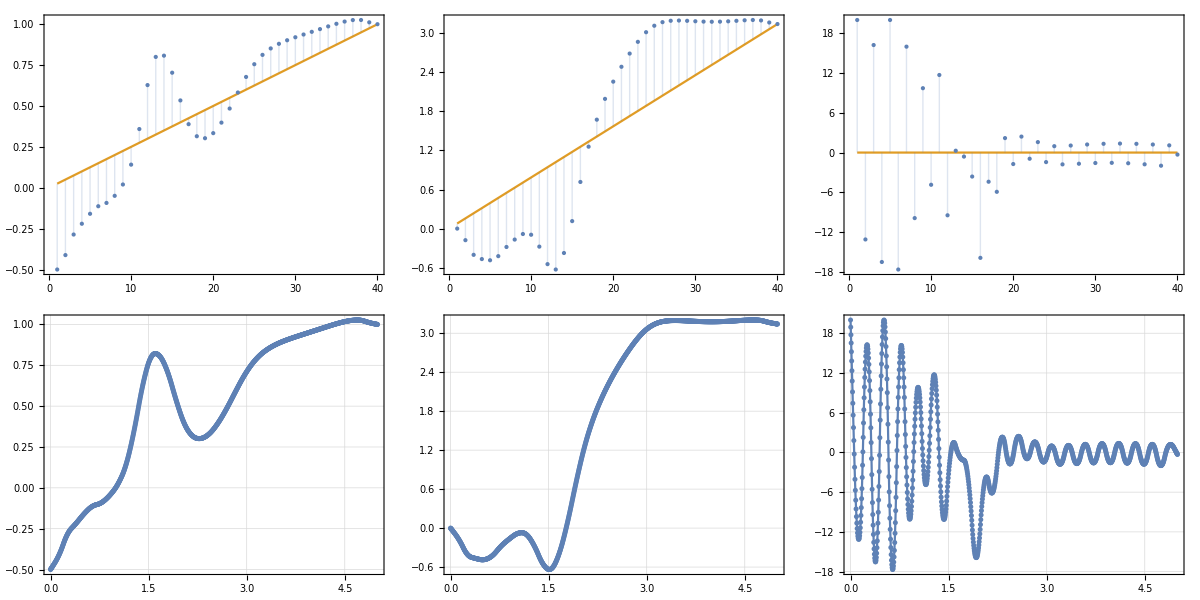

```mathematica
Block[{},
Plotter1[list_]:=ListPlot[list,PlotStyle->PointSize[Large],Axes->{False,True},Filling->{1->{2}},Joined->{False, True},Frame->True,ImageSize->Medium,PlotRange->Full];
Plotter2[list_]:=ListPlot[MapThread[{#1,#2}&,{t,list}],PlotStyle->PointSize[0.01],Axes->False,Joined->True,Frame->True,Mesh->All, InterpolationOrder->2,ImageSize->Medium,GridLines->Automatic,PlotRange->Full];
Grid[{
{Plotter1[{Values[states⟦1;;Length[t]⟧],guesses⟦1;;Length[t]⟧}],Plotter1[{Values[states⟦Length[t]+1;;2*Length[t]⟧],guesses⟦n+1;;2*Length[t]⟧}],Plotter1[{Values[states⟦-Length[t];;-1⟧],guesses⟦-Length[t];;-1⟧}]},
{Plotter2[Values[states⟦1;;Length[t]⟧]],Plotter2[Values[states⟦Length[t]+1;;2*Length[t]⟧]],Plotter2[Values[states⟦-Length[t];;-1⟧]]}
}]
]
```

## Interpolation of Solution

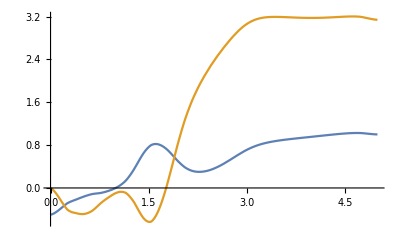

```mathematica
angles=MapThread[{#1,#2}&,{t,Values[states⟦Length[t]+1;;2*Length[t]⟧]}];
pos=MapThread[{#1,#2}&,{t,Values[states⟦1;;Length[t]⟧]}];
iAng=Interpolation[angles,Method->"Hermite"];
iPos=Interpolation[pos,Method->"Hermite"];
Plot[{iPos[x],iAng[x]},{x,0,tmax},PlotRange->Full]
```

### Quadratic Spline

```mathematica
{iPos[x],iAng[x]}/.{x->0}
```

{-0.5,0.}

## Simulation

```mathematica
responses={iPos[tt],iAng[tt]};
Grid[{{
MOVINGCART[L,responses,tmax,1.5],
Grid[{
{Style["Initial Position ",15, Italic],Style[d0,20, Italic]},
{Style["Initial Angle ",15, Italic],Style[θ0,20, Italic]},
{Style["Desired Position ",15, Italic],Style[d,20, Italic]},
{Style["Desired Angle ",15, Italic],Style[θ,20, Italic]}
},Frame->All,Alignment->{{Left,Right},{Center,Center}}]
}}]
```

| Initial Position  | -0.5
Initial Angle  | 0
Desired Position  | 1.
Desired Angle  | π